```mathematica
磁阱
```

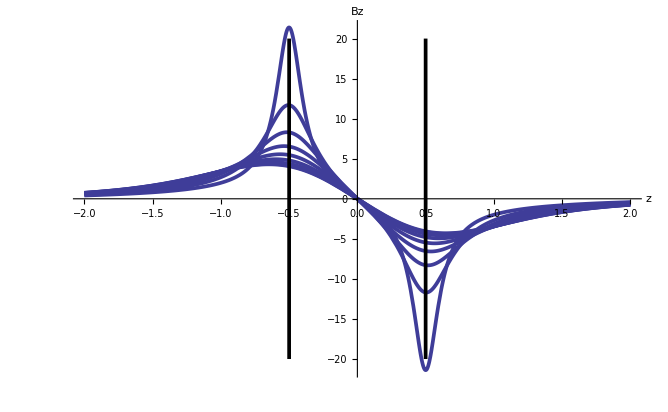

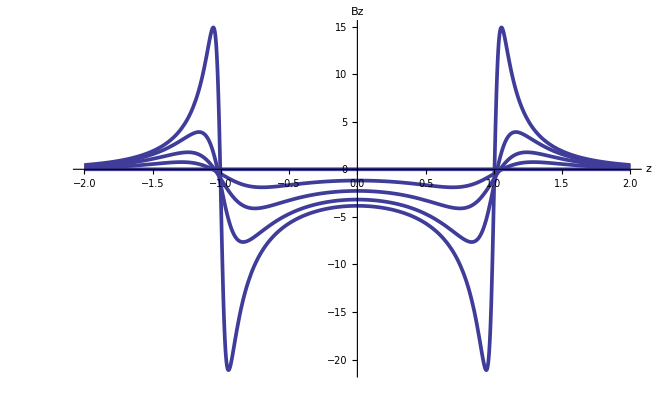

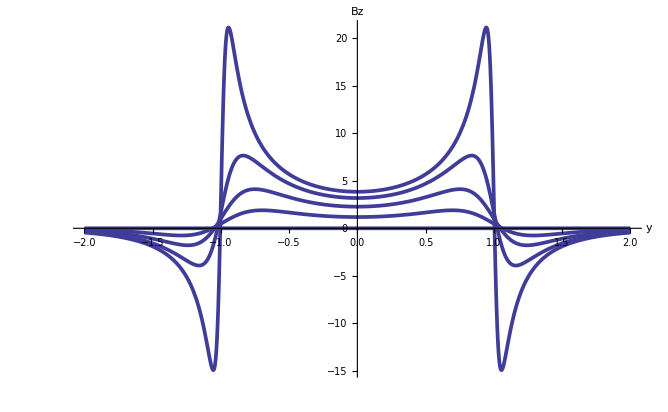

```mathematica
R=1;d=1;
By0[y_,z_]:=
NIntegrate[(R*z*Sin[φ])/((y^2+z^2+R^2-2y*R*Sin[φ])^(3/2)),
{φ,0,2π},MaxRecursion->30];
Bz0[y_,z_]:=
NIntegrate[(R*(R-y*Sin[φ]))/((y^2+z^2+R^2-2y*R*Sin[φ])^(3/2)),
{φ,0,2π},MaxRecursion->30];
(*...........................*)
By1[y_,z_]:=By0[y,z+d/2];
Bz1[y_,z_]:=Bz0[y,z+d/2];
By2[y_,z_]:=-By0[y,z-d/2];
Bz2[y_,z_]:=-Bz0[y,z-d/2];
By[y_,z_]:=By1[y,z]+By2[y,z];
Bz[y_,z_]:=Bz1[y,z]+Bz2[y,z];
(*...........................*)
fig={};
Do[
g=Plot[Bz[i R/9,z],{z,-2d,2d},PlotRange->All,
PlotStyle->Thickness[0.004]];AppendTo[fig,g],
{i,0,8}]
Show[fig,AxesStyle->Thickness[0.003],
Epilog->{Thickness[0.004],
Line/@{{{d/2,-20},{d/2,20}},
{{-d/2,-20},{-d/2,20}}}},
AxesLabel->{"z","Bz"}]
(*...........................*)
fig={};
Do[
g=Plot[Bz[y,i R/9],{y,-2R,2R},PlotRange->All,
PlotStyle->Thickness[0.004]];AppendTo[fig,g],
{i,0,4}]
Show[fig,AxesStyle->Thickness[0.003],
AxesLabel->{"z","Bz"}]
(*...........................*)
fig={};
Do[
g=Plot[Bz[y,-i R/9],{y,-2R,2R},PlotRange->All,
PlotStyle->Thickness[0.004]];AppendTo[fig,g],
{i,0,4}]
Show[fig,AxesLabel->{"y","Bz"},
AxesStyle->Thickness[0.003]]
Clear[R,d,Bz,By,By1,By2,Bz1,Bz2,g,fig]
```